```mathematica
Needs["ErrorBarPlots`"]
```

## Generating Data: particle motion

We’re doing 1D projectile motion. Set the initial y, y velocity, and set gravity!

```mathematica
y0 = 2;
vy0=3;
gdiv2=-4.9;
```

Here’s the projectile motion equation.

```mathematica
pos[t_]:=y0+vy0*t+gdiv2*t^2
```

Find out when the object lands. “landtime” only gets used to set the range of plots.

```mathematica
zeros=Solve[pos[tz]==0,tz];
landtime=tz/.zeros[[2]][[1]]
```

1.01455

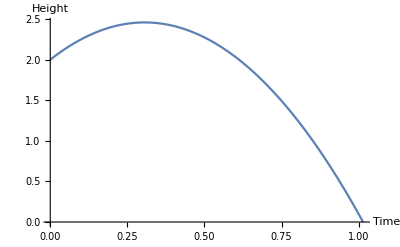

```mathematica
p1=Plot[pos[t],{t,0,landtime},AxesLabel->{"Time","Height"}]
```

## Generating noisy data

Let’s generate some noisy data. We want the data to be uncorrelated, but we want the noise to vary with time. (Open up this sub group to see how I generate the data!)

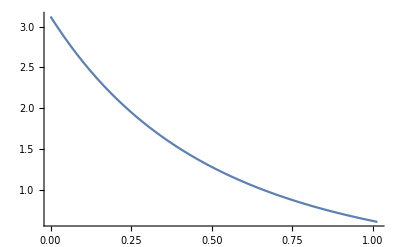

```mathematica
variance[t_]:=50/(t+2)^(4)
Plot[variance[t],{t,0,landtime}]
```

How much data should we generate? 
“samples” is how many measurements per time.
“times” is the frequency of measurements between zero and when it lands.

```mathematica
samples=300;
times=10;
```

```mathematica
dat=ConstantArray[0,{times,3}];
For[i=0,i<times,i=i+1,(dattmp=RandomVariate[NormalDistribution[pos[i/(times-1)*landtime],variance[i/(times-1)*landtime]],samples];dat[[i+1]][[1]]=i/(times-1)*landtime;
dat[[i+1]][[2]]=Mean[dattmp];
dat[[i+1]][[3]]=StandardDeviation[dattmp]/Sqrt[samples];)];
```

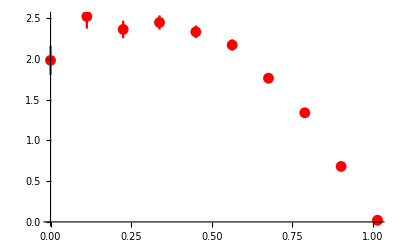

```mathematica
p2=ErrorListPlot[Table[{{dat[[i]][[1]],dat[[i]][[2]]},ErrorBar[dat[[i]][[3]]]},{i,times}],PlotStyle->Red]
```

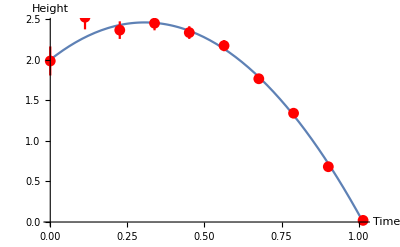

```mathematica
Show[p1,p2]
```

## Fitting!

The array “dat” constains a sequence of data with {time, height, error}. Let’s fit it to an arbitrary order polynomial.

```mathematica
polyorder=2;
```

Here, we use the “Table” command to construct the polynomial fit matrix. The extra “-1” and “+1” factors scattered about are because Mathematica 1-indexes its arrays, as opposed to C’s 0-indexing. 
The extra “If” statement is used to handle the case of computing t^0 when t = 0: Mathematica will call that indeterminate, while in reality we know t^0 is really always the constant term, so it should just equal 1.

```mathematica
fitmatrix=Table[Sum[If[row==1&&column==1,1/(dat[[i]][[3]]^2),dat[[i]][[1]]^(row-1+column-1)/(dat[[i]][[3]]^2)],{i,times}],{row,1,polyorder+1},{column,1,polyorder+1}];
fitmatrix//MatrixForm
```

(2995.38 | 2349.98 | 2028.35
2349.98 | 2028.35 | 1830.23
2028.35 | 1830.23 | 1697.03)

Here, we construct the right hand side of the fit parameter system of equations.

```mathematica
bvector=Table[{Sum[If[column==1,dat[[i]][[2]]/(dat[[i]][[3]]^2),dat[[i]][[1]]^(column-1)*dat[[i]][[2]]/(dat[[i]][[3]]^2)],{i,times}]},{column,1,polyorder+1}];
bvector//MatrixForm
```

(3111.57
1822.88
1238.94)

Solve for the fit parameters.

```mathematica
soln=Inverse[fitmatrix].bvector;
soln//MatrixForm
```

(2.06865
2.76734
-4.727)

Here is the fit polynomial:

```mathematica
fitpoly[t_]:=Sum[If[i==0,1,t^i]*soln[[i+1]][[1]],{i,0,polyorder}];
fitpoly[t]
```

2.06865+2.76734 t-4.727 t^2

Compared with the actual polynomial:

```mathematica
pos[t]
```

2+3 t-4.9 t^2

```mathematica
p3=Plot[Sum[If[i==0,1,t^i]*soln[[i+1]][[1]],{i,0,polyorder}],{t,0,landtime},PlotStyle->Green,AxesLabel->{"Time","Position"}];
```

Here:
Blue: Exact answer. (p1)
Red: Measured data. (p2)
Green: Fit data. (p3)

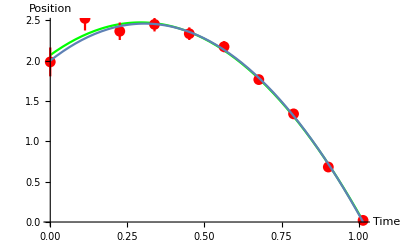

```mathematica
Show[p3,p2,p1]
```